```mathematica
G[x_, y_, en_] := I √(1/(4 en))(Exp[I Sqrt[en] Abs[x - y]] - Exp[I Sqrt[en] (x + y)])
```

```mathematica
G2[x_, y_, en_] := G[x, y, en] + (G[x, aa, en] G[aa, y, en])/(1/uu- G[aa, aa, en])
```

```mathematica
uu := 1
aa := 1
```

```mathematica
FindRoot[G[aa, aa, en]==1 / uu,{en, 10.0}]
```

{en→12.8276-7.79294 ⅈ}

```mathematica
Sqrt[12.827639304014467]
```

3.58157

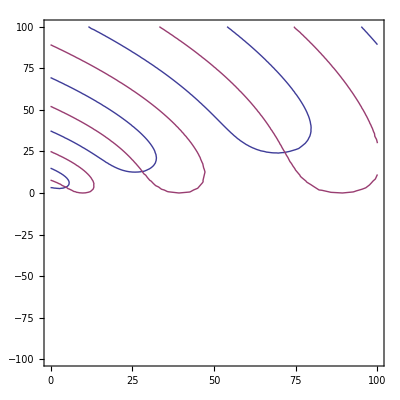

```mathematica
ContourPlot[{Re[G[aa, aa, x + I y]] == 1/ uu, Im[G[aa, aa, x + I y]] == 0.0}, {x, 0.0, 100.0}, {y, -100.0, 100.0}]
```

```mathematica
Plot3D[{1 / uu, Re[G[aa, aa, x + I y]],Im[G[aa, aa, x + I y]]}, {x, 0.0, 100.0}, {y, 0.0, 1000.0}, ImageSize->Full, Axes -> True, AxesLabel->Automatic]
```

-Graphics3D-